# Round

info@cafeplanck.com

```mathematica
Round[x]//TraditionalForm
```

Round[x]

```mathematica
Round[{-2.8,-0.3,0.3,2.3}]
```

{-3,0,0,2}

```mathematica
PiecewiseExpand[Round[x],-3<x<3]
```

Piecewise[{{-3, x<-5/2}, {-2, -5/2≤x≤-3/2}, {-1, -3/2<x<-1/2}, {1, 1/2<x<3/2}, {2, 3/2≤x≤5/2}, {3, x>5/2}, {0, True}}]

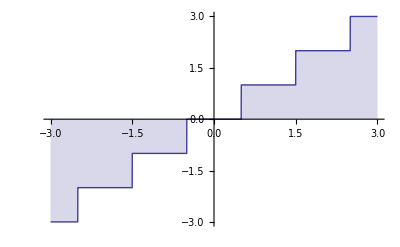

```mathematica
Plot[Round[x,1],{x,-3,3},Filling->Axis]
```

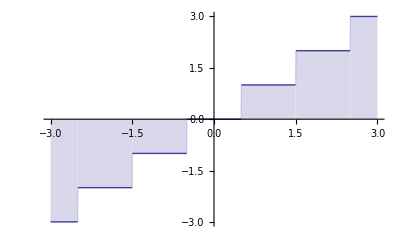

```mathematica
Plot[Round[x],{x,-3,3},Filling->Axis]
```

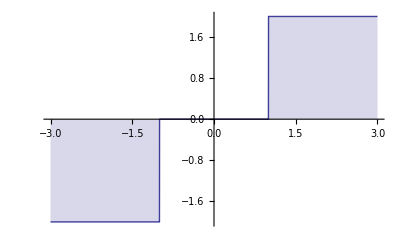

```mathematica
Plot[Round[x,2],{x,-3,3},Filling->Axis]
```